# NLIT (Not-LIT) 9/9/21

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy,LinearSolve::luc]
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5(*,1.5*)};
J0=0.5;
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.)^(-5);
dH=1;
```

```mathematica
ClearAll;
ImgSize=900;
hbarc=197.32858;
mn=938.3;
Subscript[α, fine]=1./137.;
hat[l_]:=Sqrt[2 l+1];
resultsDir="/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v4/results";
tmpDir="/home/kirscher/kette_repo/ComptonLIT/systems/tmp";
SetDirectory[resultsDir]	
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v4/results

Real32

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

dipole calculation from B. Gibson & D.R. Lehmann, PRC 13,2 (1976) (T=3/2 only!)
and Golak et al.

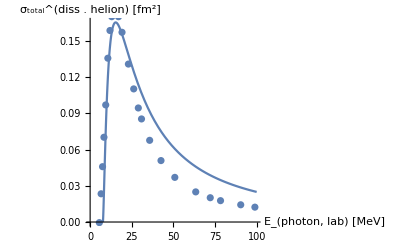

```mathematica
He3DatamBarnGolak=Import["../../../data/he3_photo_diss_sigma_golak.dat","Data"];
He3DatamBarnGibson=Import["../../../data/he3_photo_diss_sigma_gibson.dat","Data"];Bhe=7.67;
He3DataFm2=Transpose[{Transpose[He3DatamBarnGolak][[1]],Transpose[He3DatamBarnGolak][[2]] 10.^(-1)}];

σBethe[ω_,E0_,mM_]:=4 (8 Pi)/3 1./137. 1./(mM E0) (ω/E0-1)^(3./2.)/(ω/E0)^3;
Show[
Plot[hbarc^2 σBethe[ν,Bhe,938.],{ν,0,100},PlotRange->Full,AxesLabel->{"E_(photon, lab) [MeV]","σ_total^(diss . helion) [fm^2]"}],
ListPlot[He3DataFm2,PlotLabel->Style["Gibson - E1",Orange,22]]]
```

#### Orthonormalization of the basis

the function matSqrts obtains transformation matrices to a basis whose elements correspond to the
1) orthogonal Eigenvectors of the original Norm matrix
2) barring those EVs whose Eigenvalues are smaller than the chosen threshold

```mathematica
Clear[normreg,matSqrts];

matSqrts[norm_,cutoff_:0]:=Block[{μ,transf,evs,ovsqi,ovsq,n},

{μ,transf}=Transpose[Select[Sort[Transpose[Eigensystem[norm]],#1[[1]]<#2[[1]]&],#[[1]]>cutoff&]];
evs=Eigenvalues[norm];
Print["min/max: ",MinMax[evs]];
n=Length[Select[evs,#<cutoff&]];
Print["(min/max) discarded elements: ",n," ",MinMax[Select[evs,#<cutoff&]]];
Print["elements < 0: ",Length[Select[evs,#<0.&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@evs];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@evs];
(*{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}*)

trafma=(Transpose[transf].DiagonalMatrix[μ^(1/2)]);
invtrafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);
evm=(Transpose[invtrafma].norm).invtrafma;
evm=(evm+Transpose[evm])/2;(* symmetrize for stability *)
evv=Eigenvalues[evm];
Print["MinMax[Re] = ",MinMax[Re[evv]]];
Print["MinMax[Im] = ",MinMax[Im[evv]]];
(*Print[ArrayRules[SparseArray[evm]]];*)

{trafma,invtrafma}];

normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the initial state, i.e., J^π=(1/2)^+ for the helion

```mathematica
He3NormHamMat=readREAL8list["./mat_npp0.5^+"];
tmp=He3NormHamMat[[Range[1,Length[He3NormHamMat],2]]];
ActiveBasVHe3=ReadList["../basis_struct/Ssigbasv3heLIT_J0.5_npp0.5^+.dat"];
(*He3NormHamMat=tmp;*)
He3BasisDim=IntegerPart[Sqrt[Length[He3NormHamMat] 0.5]]
He3Norm=ArrayReshape[He3NormHamMat[[1;;He3BasisDim^2]],{He3BasisDim,He3BasisDim}][[;;;;dH,;;;;dH]];
He3Ham=ArrayReshape[He3NormHamMat[[He3BasisDim^2+1;;]],{He3BasisDim,He3BasisDim}][[;;;;dH,;;;;dH]];
MinMax[Eigenvalues[He3Norm]]
```

47

{0.000040212,7.18317}

```mathematica
dg=Table[He3Norm[[i,i]],{i,1,Length[He3Norm]}];Take[dg,4]
SymmetricMatrixQ[He3Norm]
```

{1.,1.,1.,1.}

True

#### The initial state (helion ground state ^3 He ) -- in Norm-Eigen-Vector Basis

other parts of this section yield analytic information on the initial state

```mathematica
{He3Nmh,He3Nmhi}=matSqrts[He3Norm,thresholdLIT];
```

min/max: {0.000040212,7.18317}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

B(^3He) = -7.14869

Dim_full^helion = 47=^!47   ;     Dim_(non - singular)^helion = 47

Norm=1.

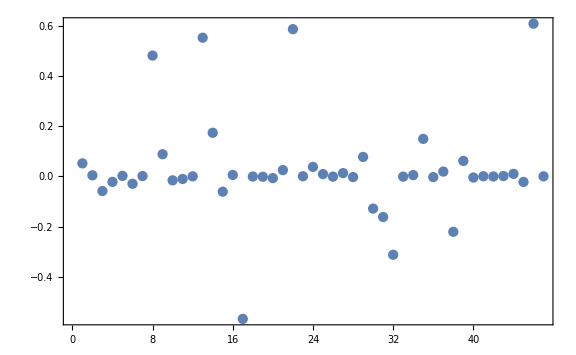
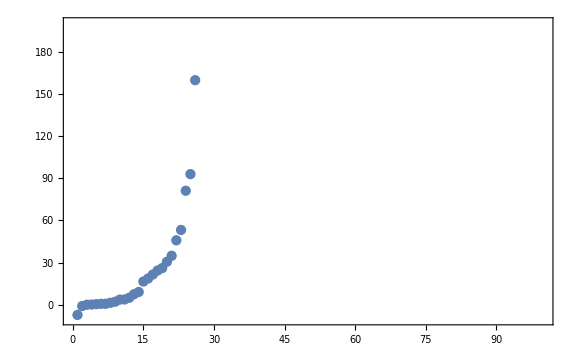
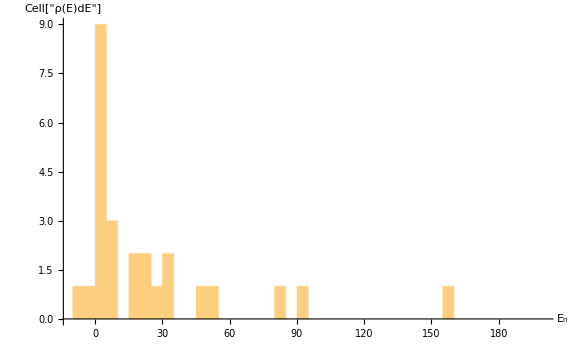
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
orderedEVSYHe3=Sort[Transpose[Eigensystem[tst=Transpose[He3Nmhi].He3Ham.He3Nmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
{e0,v0t}=orderedEVSYHe3[[1]];

dE=5;
Print["B(^3He) = ",e0];
Print["Dim_full^helion = ",Dimensions[He3Norm][[1]],"=^!",He3BasisDim,"   ;     Dim_(non - singular)^helion = ",Dimensions[v0t][[1]]]

fullv0=He3Nmhi.v0t;
Print["Norm=",fullv0.He3Norm.fullv0];
Grid[{{
ListPlot[Re[fullv0],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM basis vector}~n",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert {}^3\\text{He}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[orderedEVSYHe3[[All,1]],PlotRange->{{0,100},{-10,200}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[orderedEVSYHe3[[All,1]],{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{"Cell[TextData[{\n\" \",\nCell[BoxData[FormBox[\nSubscriptBox[\"E\", \"n\"], TraditionalForm]]]\n}]]","Cell[\"ρ(E)dE\"]"}]
}}]
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(1/2)^- or J^π=(3/2)^- for the negative-parity rank-1 E_1 operator perturbing a helion;

```mathematica
matnames=("./mat_"<>ToString[#]<>"^-")&/@Subscript[I, n];
LitNormHamMat=readREAL8list[#]&/@matnames;

ActiveBasVFin=ReadList["../basis_struct/Ssigbasv3heLIT_J0.5_0.5^-.dat"];

LITbasisDim=IntegerPart[Sqrt[Length[#] 0.5]]&/@LitNormHamMat;
Print["N_(final - full) = ",LITbasisDim[[1]]];
LitNorm=ArrayReshape[LitNormHamMat[[#]][[1;;LITbasisDim[[#]]^2]],{LITbasisDim[[#]],LITbasisDim[[#]]}][[;;;;dH,;;;;dH]]&/@Range[1,Length[Subscript[I, n]]];LitHam=ArrayReshape[LitNormHamMat[[#]][[LITbasisDim[[#]]^2+1;;]],{LITbasisDim[[#]],LITbasisDim[[#]]}][[;;;;dH,;;;;dH]]&/@Range[1,Length[Subscript[I, n]]];

LITbasisDim=Dimensions[LitNorm][[2]];
Print["N_(final - active) = ",LITbasisDim];
Print["min/max Norm EV = ",MinMax[Eigenvalues[LitNorm[[1]]]]];
```

N_(final - full) = 51

N_(final - active) = 51

min/max Norm EV = {0.175076,3.28593}

#### The final state(s) (multi-pole perturbation on the helion’s ground state ^3 He ) -- in RGM Basis

Final-state Basis dimension = {51}

min/max: {0.175076,3.28593}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-0.358725,-0.204843,0.0299077,0.0624152,0.0839329}

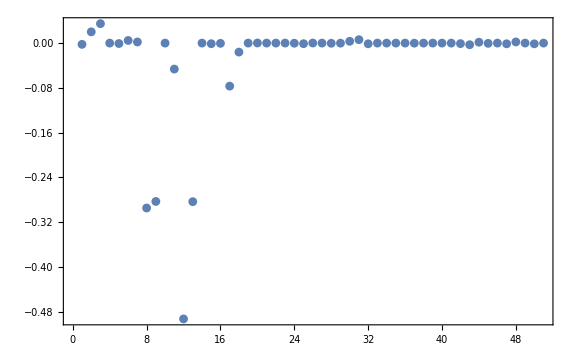
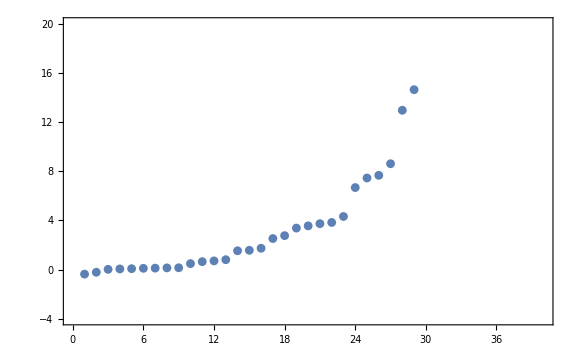
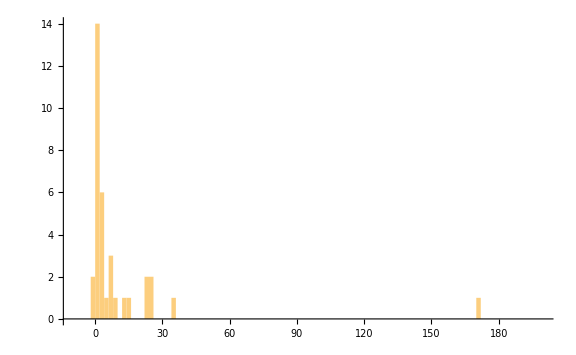
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
dE=2.;
Do[
Print["Final-state Basis dimension = ",Dimensions[LitNorm[[nj]][[1]]]];
{LitNmh,LitNmhi}=matSqrts[LitNorm[[nj]],thresholdLIT];
orderedEVSYLIT=Sort[Transpose[Eigensystem[tst=Transpose[LitNmhi].LitHam[[nj]].LitNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
{e0,v0t}=orderedEVSYLIT[[1]];

v0l=LitNmhi.v0t;
Print["Norm=",v0l.LitNorm[[nj]].v0l];
Print["lowest EV's: ",orderedEVSYLIT[[All,1]][[;;5]]];
Print[Grid[{{
ListPlot[Re[v0l],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert E_\\text{final}^{E_0+\\omega}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[#[[1]]&/@orderedEVSYLIT,PlotRange->{{0,40},{-4,20}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[#[[1]]&/@orderedEVSYLIT,{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{MaTeX["E_n",Magnification->2],MaTeX["\\rho(E)dE",Magnification->2]}]
}}]],{nj,Range[1,Length[Subscript[I, n]]]}];
```

#### Read RHS ⟨ ϕ_(lit+D3)^n|O_Lm_L|ϕ_(lit+D3)^m ⟩, n,m∈{1,N_LIT/n_k+N_D3}

the calculation is parallel in n_k parts

Normalise coupling blocks!!!!

```mathematica
CouplingBlockj={};
Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

nk=Max[ToExpression[StringSplit[FileNames["*_S_"<>JLIT<>"*"],"_"][[All,1]]]];
ks=Range[0,nk];

CouplingBlock={};
CouplingBlockT={};

Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];
	(*Why is mM unused here *)
fntmp = "InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"."<>dt;
tmp =BinaryReadList[fntmp,"Real32"];
OutDim=Dimensions[tmp][[1]]/He3BasisDim;
Print[Dimensions[tmp][[1]]];
test=ArrayReshape[tmp,{OutDim,He3BasisDim}][[;;;;dH,;;;;dH]];
AppendTo[CouplingBlockT,{mIn,test}];

,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockj,CouplingBlockT];
(*Clear[CouplingBlock];*)
,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim(⟨ψ|ο̂|helion⟩) = ",Dimensions[CouplingBlockj[[#]][[1]][[2]]&/@Range[1,Length[Subscript[I, n]]]]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Dimensions[LitHam]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Dimensions[LitNorm]];
```

3337

3337

Dim(⟨ψ|ο̂|helion⟩) = {1,71,47}

Dim(⟨ψ|Ĥ|ψ⟩) = {1,51,51}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {1,51,51}

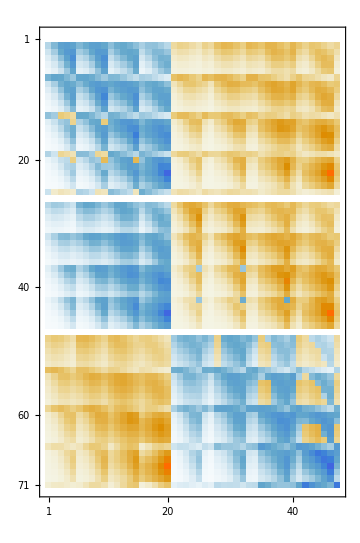
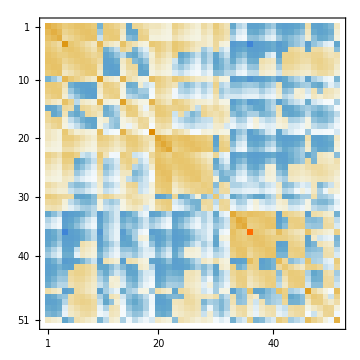
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{
MatrixPlot[Chop[CouplingBlockj[[1]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Coupling Matrix}",Magnification->2],ImageSize->Medium]
,
MatrixPlot[Chop[LitHam[[1]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Final-state Hamiltonian}",Magnification->2],ImageSize->Medium]
,
MatrixPlot[Chop[He3Ham],FrameLabel->{MaTeX["{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Helion Hamiltonian}",Magnification->2],ImageSize->Medium,PlotLegends->Automatic]
}}]
```

#### Analysis of RHS

```mathematica
(* here the active basis sizes need to be employed! *)
```

```mathematica
OμRHSEB=normreg[thresholdLIT,He3Norm];
tmp=(Transpose[OμRHSEB].He3Ham).OμRHSEB; tmp=(tmp+Transpose[tmp])/2;
{λsHeEB,trfHeEB}=Eigensystem[tmp];
evgsEB=Flatten[trfHeEB[[TakeSmallest[λsHeEB->"Index",1]]]];
inhomoEB={};evgsEB=OμRHSEB.evgsEB;
Print["ev=",TakeSmallest[λsHeEB,1][[1]]," norm=",evgsEB.He3Norm.evgsEB];
```

ev=-7.14869 norm=1.

```mathematica
inhomoEB=Table[{},{nj,Length[Subscript[I, n]]}];
Do[
OμLHSEB=normreg[thresholdLIT,LitNorm[[nj]]];
tmp=(Transpose[OμLHSEB].LitHam[[nj]]).OμLHSEB;tmp=(tmp+Transpose[tmp])/2;
{λfinalEB,trfLitEB}=Eigensystem[tmp];
Do[
tmp=CouplingBlockj[[nj]][[mm]][[2]];
AppendTo[inhomoEB[[nj]],Transpose[OμLHSEB].(tmp.evgsEB)];
,{mm,Range[1,Length[mIns[[nj]]]]}
];Print[ListPlot[inhomoEB[[1]],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert O\\Big\\vert \\text{He}3 \\right\\rangle",Magnification->2]},ImageSize->Large]]
,{nj,Range[1,Length[Subscript[I, n]]]}
];
```

Dot::dotsh: Tensors {{-0.124664,0.129502,-0.0606416,0.00726185,0.00173992,-0.209281,0.423219,-0.372995,0.185508,-0.00433399,-0.526853,0.493366,-0.265271,0.0011166,0.0261779,«22»,0.305102,-0.22803,0.166159,0.0000628724,-0.0504544,-0.969432,1.33976,-0.792458,-0.00284572,0.046135,-0.233838,-0.624688,0.44836,«1»},«49»,«1»} and {0.,-0.137691,-0.114844,-0.00686845,0.0371301,0.0123201,0.0237748,-0.518213,-0.340184,0.104554,0.184137,0.0480883,0.00647418,-0.793096,-0.169787,1.07078,«20»,-0.582938,-0.264143,0.919946,0.73693,0.160119,0.0872833,1.31918,3.53138,1.56648,0.277853,0.,0.0372919,0.0495636,0.0434471,«21»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

-Graphics-

That looks rather dodgy! Is the normalisation consistent?

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

#### Direct calculation of the (partial) strength functions

F_ν'L'νL^(I_f I_i)(k,k;E)=ρ(I_n,E) · ⟨I_f E_f||M^ν'L'(k')||I_n E ⟩⟨I_n E||M^(⋁L)(k)||I_i E_i ⟩
⇒ ρ(I_n,E)∝θ(E-E_i-k)

```mathematica
lpsisEV={};CumStrengthsEV={};

{μEV,transfEV}=Transpose[Select[Sort[Transpose[Eigensystem[He3Norm]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμRHSEV=(Transpose[transfEV].DiagonalMatrix[μEV^(-1/2)]);

{EvalsIEV,EvecsIEV}=Eigensystem[tmp=(Transpose[OμRHSEV].He3Ham).OμRHSEV;(tmp+Transpose[tmp])/2];
EvecGSiEV=OμRHSEV.Flatten[EvecsIEV[[TakeSmallest[EvalsIEV->"Index",1]]]];
EvalGSiEV=Min[EvalsIEV];
EvalGSiEV
{EvecGSiEV.He3Norm.EvecGSiEV,EvecGSiEV.He3Ham.EvecGSiEV}
```

-7.14869

{1.,-7.14869}

```mathematica
Do[

{μlEV,transflEV}=Transpose[Select[Sort[Transpose[Eigensystem[LitNorm[[nj]]]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμLHSEV=(Transpose[transflEV].DiagonalMatrix[μlEV^(-1/2)]);

{EvalsFEV,EvecsFEV}=Eigensystem[tmp=(Transpose[OμLHSEV].(LitHam[[nj]])).OμLHSEV;(tmp+Transpose[tmp])/2];
{EvalsFEV,EvecsFEV}=Sort[{EvalsFEV,EvecsFEV},#1[[1]]<#2[[1]]&];
EvecGSfEV=OμLHSEV.Flatten[EvecsFEV[[TakeSmallest[EvalsFEV->"Index",1]]]];
EvalGSfEV=Min[EvalsFEV];

Print["E_0^initial = ",EvalGSiEV,"    dim(initial) = ",Dimensions[EvalsIEV]];
Print["E_0^final  = ",EvalGSfEV,"    dim(final)   = ",Dimensions[EvalsFEV]];
tmplEV=0;

Do[
inhomoEV=Transpose[OμLHSEV].(CouplingBlockj[[nj]][[mm]][[2]].EvecGSiEV);
tmplEV=tmplEV+(EvecsFEV.inhomoEV)^2;
,{mm,Length[mIns[[nj]]]}
];
lpsisEV=Transpose[{EvalsFEV,tmplEV}];
CumStrengthsEV=Transpose[{Sort[lpsisEV][[All,1]],Accumulate[Sort[lpsisEV][[All,2]]]}];
Print[GraphicsRow[{
ListPlot[lpsisEV,Joined->False,PlotMarkers->{{♔,12},{♗,12}},PlotRange->{{-3,7.5},{0,Automatic}},Filling->Axis,FillingStyle->{{Blue},{Red}},PlotRange->{Full,Full},AxesLabel->{MaTeX["\\text{E~[MeV]}",Magnification->2],MaTeX["\\left\\langle J^\\pi_{E_n=\\omega_\\text{lab}-E_0}\\Big\\vert\\widehat{E1}\\Big\\vert\\left({}^3\\text{He}\\right)_{E_0}^{1/2^+}\\right\\rangle^2",Magnification->2]},ImageSize->ImgSize]
,
ListPlot[CumStrengthsEV,Joined->False,ImageSize->ImgSize,PlotRange->{{-3,350},{0,Automatic}},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2]]
},ImageSize->Full]]

,{nj,Range[1,Length[Subscript[I, n]]]}
]
```

E_0^initial = -7.14869    dim(initial) = {47}

E_0^final  = -0.358725    dim(final)   = {51}

Dot::dotsh: Tensors {{-0.124664,0.129502,-0.0606416,0.00726185,0.00173992,-0.209281,0.423219,-0.372995,0.185508,-0.00433399,-0.526853,0.493366,-0.265271,0.0011166,0.0261779,«22»,0.305102,-0.22803,0.166159,0.0000628724,-0.0504544,-0.969432,1.33976,-0.792458,-0.00284572,0.046135,-0.233838,-0.624688,0.44836,«1»},«49»,«1»} and {0.,-0.137691,-0.114844,-0.00686845,0.0371301,0.0123201,0.0237748,-0.518213,-0.340184,0.104554,0.184137,0.0480883,0.00647418,-0.793096,-0.169787,1.07078,«20»,-0.582938,-0.264143,0.919946,0.73693,0.160119,0.0872833,1.31918,3.53138,1.56648,0.277853,0.,0.0372919,0.0495636,0.0434471,«21»} have incompatible shapes.

Dot::dotsh: Tensors {{7.65163×10^-6,-0.000016246,8.52702×10^-6,-1.14261,0.00296187,-0.000632284,0.000188289,-0.0000520874,0.0000115364,0.165226,-0.0000836054,0.0000317481,-0.0000101141,«25»,-0.000158398,0.000141491,-0.0168633,-0.000495758,0.000149387,-0.00006463,7.76112×10^-6,0.00274828,0.000082582,-0.0000510425,-5.86943×10^-6,2.67733×10^-6,«1»},{-«22»,«49»,«1»},«48»,«1»} and {0.,-0.137691,-0.114844,-0.00686845,0.0371301,0.0123201,0.0237748,-0.518213,-0.340184,0.104554,0.184137,0.0480883,0.00647418,-0.793096,-0.169787,1.07078,«20»,-0.582938,-0.264143,0.919946,0.73693,0.160119,0.0872833,1.31918,3.53138,1.56648,0.277853,0.,0.0372919,0.0495636,0.0434471,«21»} have incompatible shapes.

Dot::dotsh: Tensors {{-0.124664,0.129502,-0.0606416,0.00726185,0.00173992,-0.209281,0.423219,-0.372995,0.185508,-0.00433399,-0.526853,0.493366,-0.265271,0.0011166,0.0261779,«22»,0.305102,-0.22803,0.166159,0.0000628724,-0.0504544,-0.969432,1.33976,-0.792458,-0.00284572,0.046135,-0.233838,-0.624688,0.44836,«1»},«49»,«1»} and {0.,-0.137691,-0.114844,-0.00686845,0.0371301,0.0123201,0.0237748,-0.518213,-0.340184,0.104554,0.184137,0.0480883,0.00647418,-0.793096,-0.169787,1.07078,«20»,-0.582938,-0.264143,0.919946,0.73693,0.160119,0.0872833,1.31918,3.53138,1.56648,0.277853,0.,0.0372919,0.0495636,0.0434471,«21»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{2531.71,1771.2,1254.31,1111.49,933.677,719.484,550.733,549.24,542.498,527.558,489.344,480.54,479.284,406.154,405.053,398.573,«19»,1.74373,1.57841,1.53856,0.814673,0.717165,0.655424,0.494525,-0.358725,-0.204843,0.15891,0.148057,0.128475,0.112003,0.0839329,0.0624152,«1»},«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {2531.71,1771.2,1254.31,1111.49,933.677,719.484,550.733,549.24,542.498,527.558,489.344,480.54,479.284,406.154,405.053,398.573,«19»,1.74373,1.57841,1.53856,0.814673,0.717165,0.655424,0.494525,-0.358725,-0.204843,0.15891,0.148057,0.128475,0.112003,0.0839329,0.0624152,«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {Transpose[{2531.71,1771.2,1254.31,1111.49,933.677,719.484,550.733,549.24,542.498,527.558,489.344,480.54,479.284,406.154,405.053,398.573,«20»,1.57841,1.53856,0.814673,0.717165,0.655424,0.494525,-0.358725,-0.204843,0.15891,0.148057,0.128475,0.112003,0.0839329,0.0624152,«1»}],«9»[2 «1»]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{2531.71,1771.2,1254.31,1111.49,933.677,719.484,550.733,549.24,542.498,527.558,489.344,480.54,479.284,406.154,405.053,398.573,«20»,1.57841,1.53856,0.814673,0.717165,0.655424,0.494525,-0.358725,-0.204843,0.15891,0.148057,0.128475,0.112003,0.0839329,0.0624152,«1»},2. «1»}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

-Graphics-

```mathematica
ListPlot[CumStrengthsEV->Range[Length[EvalsFEV]],Joined->False,ImageSize->ImgSize,PlotRange->{{-2.3,30.},{0,0.37}},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2],PlotStyle->PointSize[0.01]]
Put[CumStrengthsEV->Range[Length[EvalsFEV]],LocalObject["CumPlt2"]]
```

Transpose::nmtx: The first two levels of {Transpose[{2531.71,1771.2,1254.31,1111.49,933.677,719.484,550.733,549.24,542.498,527.558,489.344,480.54,479.284,406.154,405.053,398.573,«20»,1.57841,1.53856,0.814673,0.717165,0.655424,0.494525,-0.358725,-0.204843,0.15891,0.148057,0.128475,0.112003,0.0839329,0.0624152,«1»}],«9»[«1»]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{Transpose[{2531.71,1771.2,1254.31,1111.49,933.677,719.484,550.733,549.24,542.498,527.558,489.344,480.54,479.284,406.154,405.053,«21»,1.57841,1.53856,0.814673,0.717165,0.655424,0.494525,-0.358725,-0.204843,0.15891,0.148057,0.128475,0.112003,0.0839329,0.0624152,«1»}],Transpose[2. «1»]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[Transpose[{Transpose[{2531.71,1771.2,1254.31,1111.49,933.677,719.484,550.733,549.24,542.498,527.558,489.344,480.54,479.284,406.154,405.053,398.573,170.832,35.5186,25.7123,24.3026,23.3105,23.2195,14.6333,12.9598,8.6143,7.67248,7.45575,6.67788,4.32569,3.84104,3.74283,3.56367,3.38331,2.76996,2.53419,1.74373,1.57841,1.53856,0.814673,0.717165,0.655424,0.494525,-0.358725,-0.204843,0.15891,0.148057,0.128475,0.112003,0.0839329,0.0624152,0.0299077}],Transpose[2 (({{7.65163×10^-6,-0.000016246,8.52702×10^-6,-1.14261,0.00296187,-0.000632284,0.000188289,-0.0000520874,0.0000115364,0.165226,-0.0000836054,0.0000317481,-0.0000101141,-0.0312117,0.0000335363,-0.0000239443,-7.67757×10^-6,3.43929×10^-6,0.0061776,0.0001466,-0.0000469521,8.92906×10^-6,0.0000534967,0.000358267,-0.000201533,0.000077791,-0.0000232062,-8.11236×10^-6,5.48456×10^-6,0.0000865305,1.98794×10^-6,-1.45528×10^-6,-0.0587479,0.00334739,-0.00139403,-0.169123,0.0141503,-0.0031806,-0.000158398,0.000141491,-0.0168633,-0.000495758,0.000149387,-0.00006463,7.76112×10^-6,0.00274828,0.000082582,-0.0000510425,-5.86943×10^-6,2.67733×10^-6,-0.000348733},{-0.000509593,0.000091166,0.0000148508,-0.592984,0.0137561,-0.00409176,0.0016394,-0.00058491,0.000161806,0.0198636,0.000117872,0.0000518293,-0.0000396482,-0.00218437,0.0000406163,0.000169641,0.0000165012,1.40574×10^-6,0.000147393,-0.000319347,1.90039×10^-6,0.0000425593,0.0136914,-0.0041275,0.0016089,-0.000548529,0.00014687,0.0000597137,-0.0000381104,0.000072567,-1.61364×10^-6,6.27723×10^-6,0.0279161,-0.00166312,0.00067955,-1.23189,0.00941463,-0.00128791,0.000451059,-0.000215451,0.0959454,0.00231118,-0.000188006,0.0000541278,-5.74405×10^-7,-0.00974551,-0.000568628,0.000329988,0.0000441461,-0.0000168786,0.00118516},{0.000108451,-0.000037926,8.51655×10^-6,-0.028808,-0.0000730159,-0.000217595,-0.0000383982,0.0000390577,-0.0000200533,0.113694,-0.000181959,0.000114363,-0.0000320493,-0.250174,-0.00363411,0.00135022,0.0000260537,-4.38158×10^-7,1.05764,-0.000328895,0.000107717,-0.0000251257,0.00062386,0.000440617,0.000172105,-0.0000896508,0.0000362141,-0.00009275,0.0000214622,0.0000286907,-0.0000170679,4.30157×10^-6,0.00211395,-0.000118347,0.0000456251,-0.0110796,0.000844501,-0.000526613,0.000105656,-0.0000471496,0.0015017,-0.00032047,-0.0000918379,0.000123064,-0.0000410482,-0.000211451,-0.000025247,0.00020719,0.000146887,-0.0000528317,0.0000293007},{-0.000922415,0.000494112,-0.000176752,0.315652,-0.0143814,0.00418103,-0.00114138,0.000269929,-0.0000420777,-1.1319,0.000275222,-0.000120712,0.0000387057,0.235775,-0.0000465611,-0.0000122823,0.0000159513,-9.46685×10^-6,0.0434338,0.00284218,-0.00129636,0.000411778,0.00973809,-0.0046013,0.000837593,-0.0000669424,-0.0000402261,1.5452×10^-6,7.29699×10^-6,-0.00032858,-6.17808×10^-6,1.85691×10^-7,-0.0251048,0.00166058,-0.000634334,0.11259,-0.0194052,0.00791872,-0.00138127,0.000566993,-0.016002,0.000577988,-0.000511777,0.000462612,-0.00019162,0.00291064,-0.000106125,0.0000876579,-0.0000256598,0.000021305,-0.00035359},{0.000230182,0.0000367755,-0.0000518407,-0.00868482,-0.0174809,0.00386631,-0.00134934,0.000424794,-0.000101769,0.173218,0.00022473,-0.000162411,0.0000616426,-1.09746,0.00112708,-0.000655924,-5.06453×10^-6,-7.78372×10^-6,0.167695,-0.0008898,0.000251793,-0.0000359049,0.0189538,-0.00236927,0.000965763,-0.000357783,0.0000972801,0.000113415,-0.0000455261,-0.000143874,-0.0000138551,9.75303×10^-6,0.00445795,-0.000200554,0.000110488,-0.00430058,-0.0105666,0.00482238,-0.000534569,0.000196885,0.00114903,0.000649858,-0.000640352,0.000357,-0.000124414,-0.000263977,-0.0000581092,-0.0000809151,-0.0000874767,0.0000379694,0.0000259785},{0.00142402,-0.000977846,0.00039241,-0.00399363,0.0146703,-0.0163834,0.00387074,-0.000757976,0.0000590856,0.00206931,-0.00405213,0.00144554,-0.000392859,-0.000679676,-0.00252698,-0.00112716,-0.00041434,0.000166036,0.0000816261,0.00286849,-0.00147038,0.000536165,0.0139587,-0.0158748,0.00234976,-0.000395631,0.0000534938,-0.000334217,0.00010344,-0.00190612,0.000120442,-0.0000596004,-0.0152243,-0.0000168208,-5.3622×10^-6,-0.00493379,0.0401679,-0.00671665,0.00013894,-3.97435×10^-6,-0.103118,-0.0520178,0.00419776,-0.00236351,0.000761872,1.02136,0.0083964,-0.00371783,-0.00034513,0.0000850502,-0.106478},{-0.000844702,0.000442992,-0.000120705,0.0000645533,-0.000870153,0.00253707,-0.000441927,0.00002387,-0.0000361535,-0.000210878,-0.000307491,0.000388821,0.0000918709,0.000145354,-0.00448137,0.000969432,-0.00212606,0.000491005,-0.000032597,-0.168759,-0.641516,-0.523152,0.00157822,0.00641228,0.0711434,0.200937,0.103865,-0.0562395,-0.0121456,0.00215294,0.0146311,-0.000658138,-0.000986699,-9.74317×10^-6,-1.30313×10^-6,6.49622×10^-6,0.00115968,0.0000809578,-0.0000489742,0.0000401685,-0.000323272,0.00719809,0.00103635,-0.000492552,0.0000685113,0.000343619,-0.00120102,0.00110581,0.00180157,-0.000321034,-0.000697178},{-0.00294496,0.00139964,-0.000531632,0.000292475,-0.000653319,0.00846485,-0.00151385,0.000368578,0.000011292,-0.000804204,-0.000353029,-0.000387096,0.0000563224,0.000461277,-0.0117503,-0.00904732,0.000704503,-0.000229305,-0.0000899514,-0.89671,-0.0755301,0.63524,-0.00982708,0.067133,0.229265,-0.062575,-0.142024,0.00572253,0.030848,0.00769689,-0.000182594,-0.00633771,-0.00221288,-0.000342771,0.000194427,0.0000628904,-0.00132529,0.00245211,-0.000319508,0.000130112,-0.00236239,0.0274669,0.00224772,-0.00111335,0.000412317,0.00136368,-0.00442237,0.00653151,-0.00138025,0.000514444,-0.00243486},{-0.00260752,0.00123632,-0.000421758,0.000289543,0.00195142,0.00656218,-0.00102021,0.0000816495,0.0000633964,-0.000665387,0.000748754,-0.00028026,7.65939×10^-6,0.000299644,-0.00626297,-0.00245363,0.00077819,-0.000205069,-0.0000478608,-0.80145,1.20135,-0.894651,-0.0232898,0.0940211,0.084211,-0.252355,0.251605,0.0439605,-0.0597456,0.00390245,-0.00581087,0.0122252,-0.000321089,-0.000438102,0.000268523,0.0000890327,-0.00641363,0.00367865,-0.000495856,0.000198418,-0.00307991,0.0229296,0.00271894,-0.00123717,0.000385988,0.0012809,-0.00294623,0.00413108,-1.79719×10^-6,-0.0000571191,-0.00252089},{-0.000882995,0.000178806,-0.0000583173,-0.000113063,-0.000490002,0.0019574,0.0000731448,0.0000267423,0.0000560204,0.0000354171,-0.00185308,-0.000633057,0.000294204,-8.86254×10^-6,0.000864297,-0.002435,-0.00156861,0.000464621,2.77275×10^-6,0.00385636,-0.00217486,0.000993765,-0.000369813,0.00151586,-0.00116998,0.000642621,-0.000282284,-0.000920416,0.000410857,0.000278344,-0.00130914,0.000373706,-0.000207717,-0.0000622957,-0.0000155697,-0.000183593,-0.000105554,0.0000901268,0.0000405886,0.0000218076,-0.00221696,-0.000173533,0.00198376,-0.00141628,0.0004031,0.0771664,0.0554861,-0.025561,0.000609648,-0.000466417,-1.01188},{-0.00106733,-0.000686098,0.000554385,-0.0500154,0.0585155,-0.012058,0.00423247,-0.0011952,0.000209951,0.0226514,-0.000406825,0.000273808,-0.000102194,-0.00682158,0.000894785,-0.0000279526,-3.73046×10^-6,0.0000123221,0.00103745,0.00184708,0.000374303,-0.000499956,0.0557297,-0.0113568,0.00303346,-0.0011791,0.000452722,0.00014357,-0.00011699,0.000987171,0.0000248734,9.14388×10^-6,-1.02719,0.0832004,-0.0379056,-0.00515254,0.247355,-0.0566121,-0.00416979,0.00368528,-0.0357139,-0.00109435,0.00232235,-0.000774403,-0.0000936251,-0.00694842,-0.000282834,0.000214331,-3.02308×10^-6,0.0000336875,0.000849263},{-0.000425872,-0.0000194819,-0.0000104952,-0.000401892,0.00206017,-0.000251904,0.000407838,0.000030116,-0.0000227255,0.000176923,-0.0014569,0.000329624,-0.000108113,-0.000085386,0.000596539,-0.00277264,0.000233434,-0.0000280588,0.0000170807,0.000244624,-0.000109103,0.0000252524,0.00204927,-0.00041142,0.000115141,-0.0000228658,-0.0000211445,0.000396255,-0.000151898,-0.000158748,0.000452225,-0.0000830621,0.00898163,-0.504326,-0.619752,-0.0000697623,0.000139958,0.00373714,0.102148,0.0605341,-0.000384119,0.00178444,-0.00389232,-0.0148081,-0.00515276,-0.000330699,-0.000355882,-0.00155759,0.00250923,0.000115917,0.000101485},{-0.000602026,0.000143538,-0.0000551278,-0.000777072,0.00140426,0.000191716,0.000209947,0.0000214187,-0.0000147865,0.000368285,-0.00112919,0.000267623,-0.0000510192,-0.000129879,0.000920562,-0.00240285,-0.000253457,0.0000796428,0.0000242945,0.00046111,-0.000264247,0.0000817188,0.00135599,8.88442×10^-6,-0.0000952087,0.0000602995,-0.0000559281,0.000381367,-0.0000995088,0.000229125,-0.000068115,0.0000352316,0.00636773,-1.20966,1.15425,-0.00012704,-0.00668244,0.0208212,0.1426,-0.165539,-0.000392891,0.00176719,-0.00606133,-0.0124132,0.0214897,-0.000442388,-0.000433884,-0.000825454,0.00102859,-0.00271145,0.0000761321},{-0.526734,-0.595688,-0.251097,-0.0000159527,-0.00215825,0.0308421,0.188436,0.165266,0.0484788,0.000127575,-0.0524351,-0.0281557,-0.00723464,-0.0000831702,0.00296142,-0.0044892,0.0070457,0.0000526766,0.0000174527,0.00114111,-0.000578892,0.000198869,-0.00260232,0.00598194,-0.00151779,0.000491856,-0.00017721,-0.0000556494,0.000254648,-0.00129518,-0.0025002,0.000573984,0.000735321,0.000375367,-0.000116722,-0.000084158,-0.000321089,0.00143943,0.00028774,-0.000125136,-0.00158115,0.0144268,-0.00536527,0.00150348,-0.000367684,0.00018216,0.000711168,-0.013366,-0.00334201,0.00141036,0.000351419},{0.778818,-0.209541,-0.771572,0.0000423914,0.010404,-0.0622441,-0.214664,0.157173,0.181134,-0.000174303,0.0430641,-0.0502199,-0.0294834,0.0000847084,-0.00366864,0.000563201,0.0124199,0.00331691,-0.0000168825,-0.00141394,0.000708782,-0.000298769,0.00129714,-0.00732057,0.00208763,-0.000859768,0.00022862,0.000737241,-0.000108534,0.00601643,-0.0014869,0.000382194,-0.000536417,-0.0003237,0.000150153,0.0000838246,0.00257437,-0.00245721,0.000142906,-0.0000491857,0.00258879,-0.0211828,0.00133453,-0.000327533,-0.0000469836,-0.000325789,0.00162484,0.00498923,0.00410952,-0.00121621,-0.000301754},{0.775243,-1.21207,0.908493,0.0000803008,0.0250635,-0.099253,-0.0873673,0.275976,-0.277139,-0.000182961,0.0116806,-0.0540507,0.0677149,0.0000393211,-0.00261591,-0.00163151,0.00802355,-0.0142401,-5.54651×10^-6,-0.00137039,0.000671948,-0.000260056,-0.00193462,-0.00664879,0.00180123,-0.000699946,0.000210917,0.000334642,-0.0000664735,0.00540591,-0.000737997,0.000186226,0.000256849,-0.0002674,0.000158211,0.0000258596,0.00720433,-0.00391803,0.000583453,-0.00026003,0.00376861,-0.0231712,-0.00235487,0.00104826,-0.000322298,-0.000447631,0.00260149,-0.00151548,0.00027395,0.0000109795,-0.00017534},{0.00196928,-0.00123608,0.000509012,0.00653971,-0.153867,0.0503158,-0.0184009,0.00676947,-0.00206571,-0.00403286,-0.00206203,-0.00036205,0.000435958,0.000885208,-0.000925128,-0.00171243,-0.000169076,-0.0000235888,-0.000111612,0.000772408,-0.00036565,0.000122439,-0.163892,0.0541113,-0.0198579,0.00700177,-0.0020487,-0.000913502,0.000567093,-0.000955951,0.000121632,-0.00012468,-0.040057,0.00219727,-0.000882855,0.0543333,-0.00933526,-0.0433408,0.00611088,-0.00232342,-1.0372,-0.0293161,0.00632241,-0.00431205,0.00155962,0.0126379,0.00713183,-0.00415842,-0.000273896,0.0000167403,-0.00194702},{-0.000467201,-0.0000731259,0.000123383,-0.00185875,0.492031,-0.107907,0.0358943,-0.0132553,0.00404648,0.00128094,0.00559134,0.000684892,-0.000983713,-0.000329667,0.00336502,0.005931,0.00112946,-0.000170767,0.0000477522,-0.00116465,-0.000222718,0.000304335,0.769629,-0.183712,0.0590024,-0.0213093,0.00685022,0.00216287,-0.00175348,0.00110991,0.000324208,0.000168422,-0.0417786,0.00166551,-0.00103357,-0.00332485,1.70766,-0.502795,0.0652935,-0.0258059,0.0163812,0.0475502,0.0196979,-0.017903,0.00752357,-0.000633997,-0.0142242,0.00995355,0.00280036,-0.00143977,0.0000627025},{0.000382093,0.000539987,-0.000381806,-0.0000411778,-0.671516,0.21294,-0.0711731,0.0232141,-0.00636045,-0.000374321,0.0198126,-0.0119016,0.00452039,0.0000743662,0.04472,-0.0267782,0.000215175,-0.000704501,-3.45881×10^-6,-0.00224085,-1.63407×10^-6,0.00036601,1.02831,-0.301221,0.0893336,-0.0326732,0.0105012,0.0079066,-0.00395993,-0.0032413,-0.0015374,0.00101579,0.00455147,-0.00552479,0.00309913,0.0014001,-0.449723,0.833776,-0.158985,0.0672663,-0.00203359,0.0759115,-0.0718109,0.0563419,-0.0229315,-0.000269056,-0.0125374,0.00339068,-0.00569627,0.00341094,0.0000283878},{0.00167195,-0.000147555,-0.00010958,0.00032466,-0.680269,0.177246,-0.0539122,0.0166637,-0.00472489,-0.0000841777,0.0168895,-0.00627624,0.0023019,0.0000546798,-0.0102138,0.0094462,0.00361635,-0.00136855,-0.0000109761,0.000392072,-0.00107613,0.000613037,0.776506,-0.275932,0.0890801,-0.0339498,0.0123109,0.00137595,-0.00258448,-0.0388807,0.0016234,-0.00010971,0.00773092,0.00281632,-0.00243148,0.0000869219,0.281847,-0.97201,0.297945,-0.136317,-0.000823924,-0.0161759,0.0729764,-0.0767741,0.0356065,0.000107489,-0.000962648,0.00727456,0.00768174,-0.0050248,-8.37887×10^-6},{0.000275827,0.0000779642,-0.0000439081,-0.0000451523,-0.0649075,0.0183519,-0.00910439,0.00115697,0.0000364951,0.0000150123,0.0174946,-0.00484412,0.00118805,9.6057×10^-8,-0.00126905,0.0276692,0.00168024,-0.00070271,-4.03861×10^-7,0.0000134222,-0.0000447011,-2.733×10^-6,0.054568,-0.0165643,0.00433649,-0.00167923,0.00113782,-0.00412409,0.00105095,0.00390643,-0.0008465,0.0000228562,-0.00188903,0.0488819,-0.0302445,-0.000013466,0.0292441,-0.00752479,-1.29373,1.00492,-0.000284199,-0.0192796,0.0784231,0.133032,-0.15343,0.0000199235,0.00616367,0.0104302,-0.0146106,0.0207187,-2.73669×10^-6},{-0.000114809,-0.0000319285,0.0000111391,0.0000131813,0.022886,-0.00589024,0.0031622,-0.000136432,-0.0000474938,-3.51802×10^-6,-0.00724231,0.00153737,-0.000643811,-4.8869×10^-8,0.0019554,-0.0124115,0.00273395,-0.000504087,1.77269×10^-7,-0.0000241565,0.0000166762,-3.727×10^-6,-0.0182816,0.00609419,-0.00160837,0.000759545,-0.000439154,0.0015295,-0.000681125,-0.000770549,0.00371442,-0.000775572,0.000578155,-0.00168148,-0.0391205,1.57807×10^-6,-0.00607678,-0.0187033,0.250995,0.84857,0.0000967095,0.00792433,-0.00276222,-0.0819929,-0.10662,-6.6454×10^-6,-0.000633738,-0.00970001,0.0166813,0.00920141,2.21392×10^-6},{0.00544311,-0.00314828,0.0012267,-0.0000649911,0.256427,-0.300727,0.102407,-0.0363836,0.011785,-0.000081722,-0.0357483,0.0141689,-0.00615991,-0.0000117779,0.0819315,-0.116031,-0.00502688,0.00212451,3.05687×10^-6,0.0205255,-0.00907194,0.00366129,0.28207,-1.29497,0.774803,-0.440543,0.198944,0.0820212,-0.0664389,-0.0151768,-0.00500879,0.0118815,0.000772707,0.000218001,-0.000121221,0.000208644,0.0865176,-0.0306615,0.000439881,0.000525867,0.00419483,-0.375415,-0.0762595,0.0311172,-0.00903778,-0.0000922033,0.0175003,-0.00901846,-0.0166665,0.00649593,-4.04995×10^-6},{0.00249279,-0.000161276,-0.000329589,-0.0000687609,-1.05334,0.302271,-0.107397,0.0434528,-0.0144611,0.000393572,-0.0200126,-0.00514534,0.00490386,-0.000153851,0.0449554,-0.0656637,-0.00282951,-0.0000761011,0.0000242928,0.00477264,-0.000978221,0.000171983,-0.155355,-0.2129,0.142294,-0.0938297,0.0461372,0.0206594,-0.016524,-0.0165477,-0.00119541,0.00289061,-0.00764055,-0.00120198,0.00062953,-0.00124838,-0.161141,0.154943,-0.0181734,0.00669278,-0.0087757,-0.32517,-0.0143869,0.00406642,-0.00115784,0.000330876,0.0580221,-0.0364359,-0.0103372,0.00379911,-0.0000423944},{-0.00768062,0.00480686,-0.00203076,0.0000292267,-0.0676926,0.398347,-0.19661,0.0832363,-0.0291219,7.15767×10^-6,0.0742849,-0.0467782,0.0198572,-5.46707×10^-6,-0.0594933,-0.0157872,0.0163654,-0.00760613,9.47203×10^-7,-0.0798962,0.102297,-0.0683164,-0.0266471,0.181806,0.597157,-1.08629,0.927571,0.303427,-0.389906,0.0175141,-0.048505,0.0852648,0.000238176,-7.6562×10^-6,0.0000110249,0.0000159608,-0.0208308,0.0068494,-0.000552282,0.000154952,-0.00085668,0.380643,0.0320129,-0.0122038,0.00395184,-0.0000313351,-0.0376906,0.0495058,-0.00270271,0.000799365,6.05485×10^-6},{-0.0115659,0.0085683,-0.0037763,0.0000162197,-0.146533,0.742203,-0.415853,0.176583,-0.062549,-1.68802×10^-6,0.182777,-0.110169,0.0467839,-0.0000183139,0.0515796,-0.06818,0.028529,-0.0149737,3.42543×10^-6,-0.0246788,-0.0188324,0.0867002,0.0489637,-0.0942776,0.42481,-0.128755,-0.767812,0.119329,0.308618,-0.05254,-0.0285757,-0.0586453,0.0000572224,0.000020301,2.08665×10^-6,-1.44511×10^-6,-0.0181244,0.00811693,-0.00108943,0.000398473,-0.000661435,0.479455,0.0160716,-0.00641582,0.002344,-0.0000515536,-0.0606785,0.067731,-0.00218405,0.000344371,3.64798×10^-6},{0.00938075,-0.00743043,0.00315501,-7.66683×10^-6,0.127561,-0.637848,0.368067,-0.153796,0.0563057,6.04832×10^-6,-0.16927,0.09356,-0.0432356,0.0000157368,-0.0741381,-0.00281123,-0.00279356,0.00806087,-2.90505×10^-6,-0.0124238,0.0730365,0.0387385,-0.0566933,0.14718,-0.0907686,-0.776472,-0.22543,0.433219,0.0339563,0.0799631,-0.106284,0.0135156,-1.62243×10^-6,-6.4858×10^-6,-6.64645×10^-6,2.88031×10^-6,0.0122176,-0.00592014,0.000728637,-0.00023703,0.000415403,-0.353378,-0.0183605,0.00669213,-0.00103102,0.0000408393,0.0411888,-0.0351247,-0.0211902,0.00506137,-1.99627×10^-6},{-0.00604693,0.00680978,-0.00307723,1.7625×10^-6,-0.10987,0.614532,-0.409852,0.17138,-0.0626853,-0.0000228212,0.222583,-0.118354,0.050706,-8.2121×10^-6,0.241487,0.0297728,0.0265821,-0.0147702,1.33877×10^-6,0.0784386,0.0300921,-0.020141,0.0554605,-0.13232,-0.812169,-0.0686648,0.155961,0.141442,-0.10922,-0.19195,-0.0508427,0.0354592,0.000055855,0.000016921,-3.28274×10^-6,0.0000189162,-0.00744989,0.00156679,-0.000235522,0.0000750283,-0.000278201,0.14686,0.023185,-0.00880419,0.00223782,-0.0000266751,0.0032016,-0.00862633,0.0104746,-0.00486551,-3.01317×10^-6},{-0.0563054,0.0135754,-0.00222113,-0.0000305158,-0.000285977,-0.196703,1.02974,-0.536725,0.224596,0.0000101275,-0.593253,0.414933,-0.208139,-9.41842×10^-6,0.374246,-0.153466,-0.0876579,0.0582602,-3.23914×10^-8,0.00975184,-0.00194007,-0.000212315,0.0194054,-0.0420391,-0.0537732,0.0203424,-0.0022303,0.00793585,-0.00362301,-0.0496476,-0.0026183,0.001384,-0.000506293,0.0000884305,-0.0000373126,-0.0000849744,-0.00188218,0.0151037,-0.0014976,0.000608595,0.000438027,0.511636,-0.198009,0.0780863,-0.0215151,-0.0000873656,-0.0696273,-0.106056,-0.0626462,0.0221363,4.12153×10^-6},{0.0114972,-0.080052,0.0431508,-3.74336×10^-7,0.00407909,-0.0212921,0.0311174,1.02038,-0.78073,-1.28649×10^-6,-0.42518,-0.524782,0.61587,6.07074×10^-7,-0.00628045,-0.0437267,0.096817,-0.146198,-6.17778×10^-8,0.00284992,-0.000478431,-0.000256734,0.000741977,-0.00382611,-0.0217295,0.0084494,-0.000324094,0.00424975,5.99979×10^-6,0.248882,-0.0263202,0.00690629,0.0000182352,0.0000586273,-0.0000225062,4.46818×10^-6,0.0013075,0.000120969,0.0000563921,-0.0000106272,0.0000492473,-0.0100172,-0.0675658,0.0143604,-0.00359098,1.64701×10^-6,0.0366404,-0.159593,-0.0224045,0.00911392,-1.93224×10^-6},{-0.00719493,0.0113839,0.0653059,7.66561×10^-7,-0.00146283,0.0077169,0.107859,-0.367623,-0.765386,-6.51033×10^-7,-0.0193219,0.503182,0.503623,4.37393×10^-7,-0.0699895,0.0571707,-0.14119,-0.0815976,3.32974×10^-7,-0.000975449,0.000208573,0.000303439,-0.000546536,0.000790366,0.00784017,-0.00391149,-0.00111657,-0.0112615,0.00156615,-0.15306,0.0296721,-0.00743727,0.0000207314,-2.36146×10^-6,-5.54111×10^-6,1.01031×10^-6,-0.000219358,-0.00134816,0.000228964,-0.00010435,-0.0000246865,-0.0293399,0.00200825,0.00822205,-0.00142332,4.79696×10^-6,-0.0251207,0.0570999,-0.0113828,0.000507265,2.20011×10^-6},{-0.0281633,-0.00186026,-0.00653712,0.0000126547,-0.0295994,0.162529,0.298758,0.000887218,0.0909065,-0.0000105916,-0.190971,0.0256718,-0.081631,3.85424×10^-6,-0.69629,0.277939,0.013048,0.0136535,3.67726×10^-6,0.00100238,-0.000606686,0.000943115,0.00102088,-0.00372176,-0.00363658,0.00227749,-0.00641145,-0.0489493,0.0203612,-0.698981,-0.00833849,-0.00105609,0.000268755,0.0000873904,-0.0000670532,0.0000276551,-0.00305424,-0.0109712,0.00201815,-0.000826135,-0.00034991,-0.281521,-0.0808033,0.0632643,-0.0196718,0.0000494571,0.0631687,-0.0303338,0.00096163,0.000967958,-8.02725×10^-7},{-0.00612271,-0.00463965,0.000975108,0.0000256707,0.00350948,0.14389,-0.0157289,0.0998508,-0.0426392,-6.91645×10^-6,0.0659736,-0.108942,0.0528176,7.49658×10^-6,0.790159,-0.417386,0.00809488,-0.0119521,-6.71876×10^-6,-0.0259252,0.00471778,0.000460323,-0.0208401,0.0341368,0.171733,-0.0622043,0.0107622,0.0118224,0.00026199,-0.466647,0.00558419,-0.00335547,0.000541814,-6.87585×10^-6,0.0000245426,0.0000691223,0.00293036,-0.0129205,0.000924485,-0.000304324,-0.000427875,-0.426909,0.116024,-0.0999539,0.0349376,0.0000841054,0.229433,-0.168982,-0.0454283,0.0152658,-0.0000137197},{0.0347592,-0.0231923,0.00611969,-0.0000206715,0.0454281,-0.263508,-0.231952,0.285725,-0.125604,0.0000121435,0.474372,-0.348549,0.169519,-3.9081×10^-6,0.118329,-0.00682539,0.108786,-0.060811,-1.47932×10^-7,-0.00244414,0.000969708,-0.00038479,-0.000664754,0.00521405,0.0174245,-0.00973471,0.00439234,0.0284541,-0.0114364,-0.448225,0.0174142,-0.00452157,-0.000403005,0.000174549,-0.000124769,-0.0000467151,0.00292702,0.00855623,0.00136298,-0.000786912,0.000621396,0.301102,-0.381222,0.219335,-0.0679589,-0.0000697875,-0.949252,0.637088,-0.00262054,0.00975473,0.0000930193},{-0.0332975,0.0185962,-0.00629674,0.0000232602,-0.0481741,0.287528,0.198122,-0.205821,0.105908,-0.0000118947,-0.347268,0.314776,-0.166959,3.67962×10^-6,-0.0160207,0.0691899,-0.027441,0.0356801,-5.86792×10^-7,-0.00256805,0.00135529,-0.000564001,-0.000734099,0.00655133,0.0106249,-0.00872016,0.00464759,0.0273516,-0.0148062,0.323237,0.0349578,-0.00885691,0.000435599,-0.00015395,0.0000979277,0.0000508833,-0.00362049,-0.008885,-0.000980033,0.000511999,-0.000678974,-0.242272,0.289843,-0.152871,0.0517534,0.0000473703,-0.904013,0.523164,-0.0332617,0.0141151,0.000103782},{0.00864453,-0.011167,0.00398384,-0.0000163818,0.0259023,-0.160329,0.0378803,0.0747506,-0.0435708,9.23957×10^-6,0.332345,-0.209775,0.103568,-1.83879×10^-6,-0.000157816,0.408671,0.0819884,-0.0422645,2.49474×10^-7,0.00388058,-0.00172945,0.00114529,0.00456217,-0.00824514,-0.0163519,0.0107028,-0.0077111,-0.0822069,0.0319147,-0.0831196,0.0135847,-0.00914497,-0.000278686,-0.000729166,0.000477833,-0.0000427092,0.00990824,-0.00932235,-0.00927757,0.00513945,0.000432079,0.114387,1.31041,-0.670823,0.1911,-0.0000261435,0.0112954,0.126401,0.10725,-0.0431861,-3.37018×10^-6},{0.00107516,0.00056134,-0.000115024,-1.07752×10^-6,0.000879938,-0.00226612,-0.0138243,-0.00321508,0.00107249,1.2341×10^-6,-0.0257186,0.00993082,-0.00639731,-4.43457×10^-9,-0.000361137,-0.0991059,0.0210408,-0.00319854,-1.02025×10^-8,0.000602978,1.16818×10^-6,-0.000225143,0.000362297,-0.000212906,-0.00395598,0.000811454,0.000972518,0.0239817,-0.0136447,0.00301584,0.0254296,-0.00300845,-0.0000303244,0.0000536446,0.000330066,-2.49171×10^-6,0.00214783,-0.00507611,0.0202712,-0.00340874,5.8615×10^-6,0.00100854,0.390098,-1.52657,0.585637,2.18829×10^-7,0.00512812,-0.113142,0.230558,-0.12036,-6.84247×10^-7},{0.000250222,-0.00024953,0.0000110104,-4.98157×10^-7,0.000624434,-0.00303088,-0.000413774,0.00233293,-0.000328172,3.98665×10^-7,0.00523173,-0.00333386,0.00303945,-3.04097×10^-8,0.000183851,0.00313134,-0.0157837,0.00320226,-1.48628×10^-9,0.000128619,-0.000100178,-0.0000332095,0.000173884,-0.000235036,-0.000574902,0.000720702,0.0000242824,0.00188774,0.00201683,-0.00105297,-0.0172998,0.0037409,-0.000010329,0.000128452,-0.00037005,-1.19663×10^-6,0.000617835,-0.00116032,0.0104215,-0.0238886,8.91815×10^-6,0.00207396,0.0303532,-0.391937,1.21807,-4.03108×10^-7,0.00178488,0.00713397,-0.0018007,-0.170798,-3.14315×10^-7},{-0.000677454,-0.000424027,0.000697867,-3.26596×10^-6,0.00239066,-0.0174139,0.0248827,-0.00908869,-0.00153088,-3.06654×10^-7,0.0324985,-0.0684,0.035196,1.93238×10^-8,0.030455,-0.57982,0.0303543,-0.0165371,-3.09849×10^-7,0.00799463,-0.0188119,0.0032858,0.00339035,-0.015577,-0.0149488,0.0847339,-0.0263274,1.0372,-0.820481,-0.00369481,-0.280753,0.296745,-0.0000368217,-0.0000507175,0.0000190268,-4.76728×10^-6,0.00143672,-0.00036863,-0.000790727,0.000223811,0.0000828935,0.00633428,0.00448853,0.023096,-0.0095664,-1.62806×10^-6,0.00285515,-0.0452392,-0.0930341,0.0296148,-5.46854×10^-7},{-0.000276543,-0.000700773,-0.000432403,1.66581×10^-6,-0.0029327,0.0161881,-0.00974959,0.016371,-0.00141064,-2.38569×10^-7,0.034725,0.0529507,-0.0300821,-1.80542×10^-7,-0.034632,0.562311,-0.00935797,0.0100266,4.00347×10^-7,-0.00352328,-0.00288299,0.0216063,0.000415494,0.00068651,0.0314368,-0.020169,-0.0895394,-0.172099,-0.816426,0.00151422,0.195965,0.238114,0.0000242172,0.0000480008,-0.0000176021,2.76726×10^-6,-0.000516614,-4.58509×10^-6,0.000575205,-0.000162471,-0.0000331379,-0.00420325,0.0121889,-0.02404,0.00984211,6.91291×10^-7,-0.0208958,0.285855,0.141751,-0.0440024,3.48846×10^-6},{-0.00279076,-0.00177985,0.00022863,1.8345×10^-6,-0.0038645,0.0217233,0.0188981,0.0197218,-0.00717995,-7.87782×10^-7,0.159814,0.0194299,-0.0308702,3.42056×10^-8,-0.0496372,0.709984,0.134488,-0.0253493,5.24232×10^-7,-0.00170726,-0.00948819,-0.00985707,0.000646618,0.00115683,0.0178005,0.0552801,0.0344708,0.488454,0.142682,0.00251468,-0.202318,-0.0227378,0.000033945,0.0000631867,-0.0000178535,3.36587×10^-6,-0.000574227,-0.000128273,0.000668947,-0.0000803607,-0.0000398337,-0.00198548,0.0309273,-0.0377891,0.012058,-5.24067×10^-7,-0.0624353,0.734351,0.106203,-0.0370977,0.0000103318},{-0.00904595,-0.00186077,0.00115729,-1.96529×10^-6,0.00130071,-0.00911877,0.123742,-0.0230617,0.00514237,-1.08704×10^-6,0.367686,-0.209814,0.106127,8.83632×10^-7,0.0245583,-0.322948,0.145134,-0.0785932,-4.37101×10^-7,0.0044243,0.00737145,0.000533345,0.0000737857,-0.00164666,-0.0339978,-0.0303117,0.00197308,-0.222933,0.0615432,0.0022699,0.233544,-0.0823251,-5.7773×10^-6,-1.91555×10^-6,5.40559×10^-6,-2.60261×10^-6,0.000586084,-0.000345311,0.0000588889,-0.0000153957,0.0000217433,0.00227895,-0.00380854,0.00773055,-0.00333654,-1.73442×10^-6,-0.0992207,0.930458,-0.0686305,0.0488623,0.0000171018},{-0.00226557,0.0201065,0.0347226,1.11723×10^-7,-0.000789716,0.00469764,0.00200386,-0.294664,-0.282949,1.1954×10^-7,-0.0464279,-0.492802,-0.283337,-1.15799×10^-7,-0.00110523,-0.00044421,-0.0768691,-0.0160863,3.37271×10^-8,0.000211371,0.0000114594,-8.59057×10^-6,0.0000514709,-0.000231348,-0.00104566,0.000114594,9.45272×10^-6,-0.000327476,-0.0000982972,0.00320368,0.00609542,-0.00125608,-4.09473×10^-6,-2.7058×10^-6,5.94547×10^-7,-1.94038×10^-7,-0.000143768,-0.0000425655,0.0000215275,-0.0000158763,-9.80466×10^-6,-0.000939949,-0.00289739,0.0015745,-0.000458747,4.42244×10^-7,-0.0012294,0.00204827,0.0000172664,-0.0012946,2.4351×10^-7},{-0.0134871,-0.0377505,0.0300718,-1.10622×10^-6,0.00243286,-0.0133782,0.246053,0.282436,-0.350206,-1.32512×10^-6,0.463015,0.223008,-0.541499,1.17594×10^-6,0.000640463,0.00889009,-0.00556843,-0.109989,-2.30272×10^-7,-0.00101524,6.6641×10^-6,-0.0000287127,-0.00045292,0.00114514,0.00488171,-0.000660097,0.000325319,-0.000397911,-0.000116989,-0.0043842,0.0141653,-0.00513076,0.0000363983,0.0000159984,-5.17444×10^-6,-9.87925×10^-7,0.000678376,0.0000123985,0.0000386888,-0.0000104534,0.0000286407,-0.00304282,0.0024764,-0.00143222,0.00081535,-4.47309×10^-8,0.00669658,-0.0242922,-0.0560456,0.0212997,-9.05605×10^-7},{0.02108,-0.0149724,0.00173603,-9.62948×10^-7,0.00478054,-0.022492,-0.21437,0.224598,-0.0838442,1.90225×10^-6,-0.364249,0.573199,-0.308397,-8.38579×10^-7,0.0103497,-0.0746198,-1.02857,0.552702,3.28246×10^-8,0.00121057,-0.00029416,-0.000216463,-0.0000406294,-0.00149277,-0.00556457,0.00268905,0.000444491,0.00363967,0.00130883,-0.00910545,0.0271875,-0.00881163,-0.0000545854,-0.0000186161,0.0000280238,-1.4116×10^-6,0.000661523,-0.000121137,-0.000293548,0.000138076,0.0000598741,0.0109315,0.00906167,0.0080743,-0.00146856,-2.53311×10^-6,-0.00106862,0.030379,-0.886335,0.295714,-3.47794×10^-7},{-0.0139344,0.0153327,-0.00762033,6.64648×10^-7,-0.00343047,0.0162548,0.13018,-0.193379,0.131376,-1.11149×10^-6,0.17864,-0.427217,0.395084,4.42779×10^-7,-0.00463092,0.0246395,0.258338,-0.541931,-2.62664×10^-8,-0.00102165,-0.000849051,0.00146015,0.000154307,0.000298891,0.00734186,0.000579309,-0.0066389,0.00856975,-0.0140748,0.0065619,-0.442866,0.131495,0.0000332654,0.0000219214,0.0000110804,8.70178×10^-7,-0.000452207,0.0000547168,0.000154968,-0.0000299514,-0.0000420961,-0.00829134,-0.0134405,0.0165609,-0.00468055,2.0726×10^-6,0.00163372,-0.0313491,-1.03934,0.432062,9.3613×10^-8},{0.0095993,-0.00733539,0.0136999,-4.12672×10^-7,0.00227437,-0.0105785,-0.0927265,0.081177,-0.16479,9.24519×10^-7,-0.141068,0.11337,-0.416398,-3.98696×10^-7,0.00355335,-0.0186434,0.554197,0.543306,3.07948×10^-8,0.000185071,0.000316457,0.00164145,-0.0000481915,-0.000459582,-0.000320739,-0.00425874,-0.00684857,-0.00784302,-0.010614,-0.00500887,-0.479685,0.149843,-0.0000247893,-4.20381×10^-6,6.56304×10^-6,-6.3677×10^-7,0.000328623,-0.000097501,-0.000140849,0.0000603436,0.0000280652,0.00503735,0.00667918,0.0029148,-0.00213207,-1.21686×10^-6,-0.00313378,0.0337388,-0.322942,0.251417,3.42605×10^-7},{-0.000352878,-0.000246401,0.000896474,4.06498×10^-8,-0.0000349031,0.000189657,0.00479135,-0.000384556,-0.00872416,-1.78237×10^-8,0.0111619,-0.00866931,-0.0190174,1.52951×10^-8,-0.000419059,0.00476594,0.0632693,0.0244626,1.94866×10^-9,-0.000185516,0.000427902,0.000806916,-0.0000347055,0.000206503,0.000769824,-0.00361458,-0.00310744,-0.00606399,-0.00432291,0.0000249831,-0.232718,0.0774599,1.63348×10^-6,-0.0000148925,0.0000271073,1.73605×10^-8,-4.00031×10^-6,-0.0000105987,0.0000376471,-0.0000396564,-8.9269×10^-7,-0.000150007,0.00170962,-0.00850257,0.0160848,3.39721×10^-8,0.000652618,-0.00435201,0.354346,-1.1725,-1.13582×10^-7},{0.000315429,0.00236598,0.0022967,-1.30549×10^-7,-0.000029859,0.0000433646,-0.0069421,-0.0292928,-0.0168738,3.19879×10^-9,-0.0201368,-0.0767186,-0.0270651,-2.66786×10^-8,0.000919986,-0.00954564,0.16177,0.0813564,-6.10862×10^-9,0.000783915,-0.0023756,-0.00266186,0.000233284,-0.00110955,-0.00225764,0.0172427,0.0091753,0.0215023,0.0115513,0.000101141,1.00921,-0.527274,-3.44136×10^-6,2.96272×10^-6,5.44407×10^-6,-1.5766×10^-7,0.0000574005,-0.000051988,0.0000280625,-0.0000131612,2.89885×10^-6,0.000112894,0.000727173,0.000717609,0.00184243,-3.21574×10^-8,-0.00430206,0.0300358,-0.0292372,-0.123883,8.07353×10^-7},{0.000348059,-0.000619529,-0.000403187,-6.53782×10^-8,0.0000259697,-0.000330001,-0.00311647,0.00869543,0.00180724,2.33778×10^-9,-0.00342787,0.021912,0.000583376,-2.22184×10^-8,-0.000182129,0.00283646,-0.0299579,-0.0191874,6.89201×10^-9,0.000105894,-0.000734718,0.00378005,0.000170421,-0.000685768,0.00161633,-0.00100539,-0.0187776,-0.0127283,-0.0121511,-0.000204947,-0.00182356,-0.987618,-1.075×10^-6,-8.17644×10^-7,-9.18753×10^-7,-7.63264×10^-8,0.0000435715,-0.0000116941,-8.18699×10^-6,5.73158×10^-6,2.84253×10^-6,0.0000946014,0.000468344,-0.000515377,-0.000248093,-2.15979×10^-8,0.000745882,-0.00399527,0.0160099,0.0155586,-1.4326×10^-7},{0.0300305,-0.0108801,0.00169548,-5.35001×10^-7,0.0046194,-0.0209747,-0.332191,0.217736,-0.0936221,2.59353×10^-6,-0.525081,0.493665,-0.296065,-1.35593×10^-6,0.00816852,-0.0463551,0.461474,-0.714701,1.53533×10^-7,0.00151572,0.0000956877,-0.0000272041,0.0000619411,-0.00157325,-0.00756794,0.000728386,-0.000128012,-0.00160231,0.000662207,-0.00988597,-0.015619,0.0127045,-0.0000721814,-0.0000265998,0.0000120277,-8.3917×10^-7,0.000509738,-0.000168674,-0.000302018,0.000119458,0.0000580695,0.0138172,0.0164804,-0.0052067,0.00139072,-3.09404×10^-6,-0.00743468,0.0700178,0.0866244,-0.0371605,6.32182×10^-7}}.{0.,-0.137691,-0.114844,-0.00686845,0.0371301,0.0123201,0.0237748,-0.518213,-0.340184,0.104554,0.184137,0.0480883,0.00647418,-0.793096,-0.169787,1.07078,0.775925,0.165071,-0.00211345,0.0139925,1.29529,3.53139,1.55254,0.273848,0.00668185,0.,-0.135402,-0.304155,-0.472553,-0.252952,-0.0474865,-0.61371,-0.833052,-0.661507,-0.140157,-0.00883325,-0.582938,-0.264143,0.919946,0.73693,0.160119,0.0872833,1.31918,3.53138,1.56648,0.277853,0.,0.0372919,0.0495636,0.0434471,0.0239305,0.00849193,-0.025373,0.462915,0.390047,0.192852,0.0569688,0.0143041,0.110762,0.599677,0.339997,-0.41101,-0.426381,-0.17326,-0.0753219,-0.573388,-1.84554,-3.53216,-2.10379,-0.736629,-0.0273556}))^2]}]→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51},Joined→False,ImageSize→900,PlotRange→{{-2.3,30.},{0,0.37}},AxesLabel→{-Graphics-,-Graphics-},PlotLabel→-Graphics-,PlotStyle→PointSize[0.01]]

LocalObject[file:///home/kirscher/.Wolfram/Objects/CumPlt2]

```mathematica
pltWeCoul=Get[LocalObject["CumWeCoul"]];
pltBliCoul=Get[LocalObject["CumPlt"]];
pltBliCoul2=Get[LocalObject["CumPlt2"]];
ListPlot[{pltWeCoul,pltBliCoul,pltBliCoul2},Joined->False,ImageSize->ImgSize,PlotRange->{{-2.3,30.},{0,0.37}},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2],PlotStyle->PointSize[0.01],PlotLegends->{"with","w/o","w/o poly grd"}]
```

-Graphics-

Part::partw: Part {45,46} of «1» does not exist.

Part::partw: Part 46 of {0.0640857,{0.349071,-0.816416,-0.00763496,0.00851436,-0.00385928,0.00560881,0.459822}} does not exist.

Dot::rect: Nonrectangular tensor encountered.

Part::pkspec1: The expression {{0.00437113,0.0058956,0.0907056,0.608827,0.782443,-0.0938368,0.00509327},{0.474043,0.711195,0.00035803,0.00256579,-0.0131571,0.00228848,0.519918},«3»,{0.0172314,4.0009×10^-6,0.00899877,0.789648,-0.611638,0.0297973,-0.0330414},{0.767266,1.52342×10^-6,-0.000698049,-0.0275263,0.02154,-0.00172833,-0.641762}}.46 cannot be used as a part specification.

Dot::rect: Nonrectangular tensor encountered.

Part::partw: Part {2,3,4} of {{0.00437113,0.0058956,0.0907056,0.608827,0.782443,-0.0938368,0.00509327},{0.474043,0.711195,0.00035803,0.00256579,-0.0131571,0.00228848,0.519918},«3»,{0.0172314,4.0009×10^-6,0.00899877,0.789648,-0.611638,0.0297973,-0.0330414},{0.767266,1.52342×10^-6,-0.000698049,-0.0275263,0.02154,-0.00172833,-0.641762}}.{«20»,«1»} does not exist.

Part::partw: Part {4,5,6} of {{0.00437113,0.0058956,0.0907056,0.608827,0.782443,-0.0938368,0.00509327},{0.474043,0.711195,0.00035803,0.00256579,-0.0131571,0.00228848,0.519918},«3»,{0.0172314,4.0009×10^-6,0.00899877,0.789648,-0.611638,0.0297973,-0.0330414},{0.767266,1.52342×10^-6,-0.000698049,-0.0275263,0.02154,-0.00172833,-0.641762}}.{«20»,«1»} does not exist.

Part::partw: Part {2,3,4} of {{0.00437113,0.0058956,0.0907056,0.608827,0.782443,-0.0938368,0.00509327},{0.474043,0.711195,0.00035803,0.00256579,-0.0131571,0.00228848,0.519918},«3»,{0.0172314,4.0009×10^-6,0.00899877,0.789648,-0.611638,0.0297973,-0.0330414},{0.767266,1.52342×10^-6,-0.000698049,-0.0275263,0.02154,-0.00172833,-0.641762}}.46 does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part {2,3,4,5,6} of {{0.00437113,0.0058956,0.0907056,0.608827,0.782443,-0.0938368,0.00509327},{0.474043,0.711195,0.00035803,0.00256579,-0.0131571,0.00228848,0.519918},«3»,{0.0172314,4.0009×10^-6,0.00899877,0.789648,-0.611638,0.0297973,-0.0330414},{0.767266,1.52342×10^-6,-0.000698049,-0.0275263,0.02154,-0.00172833,-0.641762}}.{«20»,«1»} does not exist.

Part::pkspec1: The expression {{0.00437113,0.0058956,0.0907056,0.608827,0.782443,-0.0938368,0.00509327},{0.474043,0.711195,0.00035803,0.00256579,-0.0131571,0.00228848,0.519918},«3»,{0.0172314,4.0009×10^-6,0.00899877,0.789648,-0.611638,0.0297973,-0.0330414},{0.767266,1.52342×10^-6,-0.000698049,-0.0275263,0.02154,-0.00172833,-0.641762}}.46 cannot be used as a part specification.

ListPlot::lpn: «1» is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression {{0.00437113,0.0058956,0.0907056,0.608827,0.782443,-0.0938368,0.00509327},{0.474043,0.711195,0.00035803,0.00256579,-0.0131571,0.00228848,0.519918},«3»,{0.0172314,4.0009×10^-6,0.00899877,0.789648,-0.611638,0.0297973,-0.0330414},{0.767266,1.52342×10^-6,-0.000698049,-0.0275263,0.02154,-0.00172833,-0.641762}}.46 cannot be used as a part specification.

ListPlot::lpn: «1» is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression {{0.00437113,0.0058956,0.0907056,0.608827,0.782443,-0.0938368,0.00509327},{0.474043,0.711195,0.00035803,0.00256579,-0.0131571,0.00228848,0.519918},«3»,{0.0172314,4.0009×10^-6,0.00899877,0.789648,-0.611638,0.0297973,-0.0330414},{0.767266,1.52342×10^-6,-0.000698049,-0.0275263,0.02154,-0.00172833,-0.641762}}.46 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: «1» is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partw: Part {2,3,4} of {{0.00437113,0.0058956,0.0907056,0.608827,0.782443,-0.0938368,0.00509327},{0.474043,0.711195,0.00035803,0.00256579,-0.0131571,0.00228848,0.519918},«3»,{0.0172314,4.0009×10^-6,0.00899877,0.789648,-0.611638,0.0297973,-0.0330414},{0.767266,1.52342×10^-6,-0.000698049,-0.0275263,0.02154,-0.00172833,-0.641762}}.46. does not exist.

Part::partw: Part {4,5,6} of {{0.00437113,0.0058956,0.0907056,0.608827,0.782443,-0.0938368,0.00509327},{0.474043,0.711195,0.00035803,0.00256579,-0.0131571,0.00228848,0.519918},«3»,{0.0172314,4.0009×10^-6,0.00899877,0.789648,-0.611638,0.0297973,-0.0330414},{0.767266,1.52342×10^-6,-0.000698049,-0.0275263,0.02154,-0.00172833,-0.641762}}.46. does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

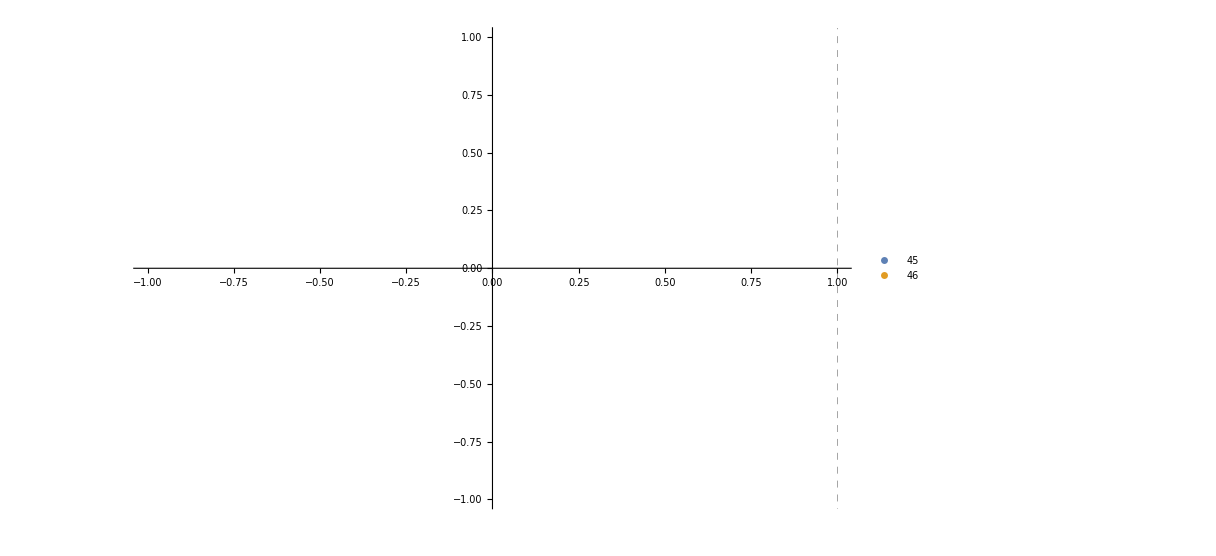
ListPlot[({{0.00437113,0.0058956,0.0907056,0.608827,0.782443,-0.0938368,0.00509327},{0.474043,0.711195,0.00035803,0.00256579,-0.0131571,0.00228848,0.519918},{-0.000528031,0.00216092,-0.708557,0.0201956,-0.0188502,-0.705121,0.000541328},{0.00442258,-0.00677469,0.702697,-0.0682739,-0.112208,-0.699207,0.00513343},{0.474043,-0.711186,-0.00773674,0.00832901,-0.00566275,0.00602887,0.519918},{0.0172314,4.0009×10^-6,0.00899877,0.789648,-0.611638,0.0297973,-0.0330414},{0.767266,1.52342×10^-6,-0.000698049,-0.0275263,0.02154,-0.00172833,-0.641762}}.{0.0640857,{0.349071,-0.816416,-0.00763496,0.00851436,-0.00385928,0.00560881,0.459822}})⟦{{0.00437113,0.0058956,0.0907056,0.608827,0.782443,-0.0938368,0.00509327},{0.474043,0.711195,0.00035803,0.00256579,-0.0131571,0.00228848,0.519918},{-0.000528031,0.00216092,-0.708557,0.0201956,-0.0188502,-0.705121,0.000541328},{0.00442258,-0.00677469,0.702697,-0.0682739,-0.112208,-0.699207,0.00513343},{0.474043,-0.711186,-0.00773674,0.00832901,-0.00566275,0.00602887,0.519918},{0.0172314,4.0009×10^-6,0.00899877,0.789648,-0.611638,0.0297973,-0.0330414},{0.767266,1.52342×10^-6,-0.000698049,-0.0275263,0.02154,-0.00172833,-0.641762}}.46⟧⟦All,{2,3,4,5,6}⟧,Joined→True,GridLines→{{2,4,6},None},GridLinesStyle→Directive[RGBColor[1, 0.5, 0],Dashing[{Small,Small}],Thickness[Large]],PlotLegends→{45,46},ImageSize→900,PlotRange→{All,Automatic}] | -Graphics-

```mathematica
InitialStateFrags=Flatten[Import[resultsDir<>"/../basis_struct/LITbas_dims_J0.5_npp0.5^+.dat","Table"]];
FinalStateFrags=Flatten[Import[resultsDir<>"/../basis_struct/LITbas_dims_J0.5_0.5^-.dat","Table"]];
zerlPERfrag=1;
Length[FinalStateFrags];
Total[FinalStateFrags];
ArrayReshape[FinalStateFrags,{Length[FinalStateFrags]/zerlPERfrag,zerlPERfrag}];
gl={Accumulate[FinalStateFrags],None};
f1=1;
f2=3;Min[12,Length[FinalStateFrags]];
BVrange=Range[Accumulate[FinalStateFrags][[f1]],Accumulate[FinalStateFrags][[f2]]];
selectionInices={45,46};(*{14,15};*)
selectionEVs=Sort[Transpose[{EvalsFEV,EvecsFEV}],#1[[1]]<#2[[1]]&][[selectionInices]][[All,2]];
selectionEVs2=(OμLHSEV.#)^1&/@selectionEVs;
fragRange=Table[Range[Prepend[gl[[1]],1][[n]],Prepend[gl[[1]],1][[n+1]]],{n,1,Length[gl[[1]]]}];
frgStr=Table[Total[selectionEVs2[[nn]][[#]]]&/@fragRange,{nn,Length[selectionInices]}];
Grid[{{
ListPlot[selectionEVs2[[All,BVrange]],Joined->True,GridLines->gl,GridLinesStyle->Directive[Orange,Dashed,Thick],PlotLegends->selectionInices,ImageSize->ImgSize,PlotRange->{All,Automatic}],
ListPlot[frgStr,Joined->False,GridLines->{Range[Length[gl[[1]]]],None},GridLinesStyle->Directive[Gray,Dashed,Thick],PlotLegends->selectionInices,ImageSize->ImgSize]
}}]
```